```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-20,10];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

```mathematica
pt2to3={0,0.2,0.5,1,2,3,4,5,7,10,12,15,17,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,200,300,400,500,600,700,800,900,1000};
pt2to4={0,0.2,0.5,1,2,3,4,5,7,10,12,15,17,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,200,300,400,500,600,700,800,900,1000};
```

## c1=c2=c3=1, fa=10 TeV

#### input data

```mathematica
xs2to3={10.86,7.1,5.9,4.98,4.18,3.75,3.46,3.24,2.93,2.61,2.46,2.27,2.17,2.06,1.89,1.76,1.65,1.56,1.489,1.414,1.358,1.302,1.252,1.203,1.165,1.123,1.088,1.051,1.023,0.99(*100GeV*),0.604,0.409,0.293,0.219,0.166,0.127,0.099,0.0775,0.061}*10^-6/100(*rescale fa from 1TeV to 10TeV*);
xs2to4={9.32,7.08,6.64,6.35,6.02,5.82,5.67,5.59,5.41,5.23,5.14,5.02,4.96,4.89,4.77,4.65,4.58,4.49,4.40,4.34,4.26,4.21,4.15,4.09,4.03,4.00,3.92,3.88,3.83,3.78(*100GeV*),3.07,2.58,2.23,1.95,1.73,1.53,1.36,1.225,1.098}*10^-7/100(*rescale fa from 1TeV to 10TeV*);

xs2to4data=Table[{pt2to4[[i]],xs2to4[[i]]},{i,1,Length[pt2to4]}];
VBSdata={{-10,7.36*10^-10/100*1/(2.16*10^-3)+2.18*10^-10/100*1/(2.16*10^-3)},{10000,7.36*10^-10/100*1/(2.16*10^-3)+2.18*10^-10/100*1/(2.16*10^-3)}};
VBSwadata={{-10,7.36*10^-10/100*1/(2.16*10^-3)},{10000,7.36*10^-10/100*1/(2.16*10^-3)}};
VBSwzdata={{-10,2.18*10^-10/100*1/(2.16*10^-3)},{10000,2.18*10^-10/100*1/(2.16*10^-3)}};
xs2to3data=Table[{pt2to3[[i]],xs2to3[[i]]},{i,1,Length[pt2to3]}];
VBFdata={{-10,5.39*10^-6/100+2*1.5*10^-7/100+8.5*10^-8/100},{10000,5.39*10^-6/100+2*1.5*10^-7/100+8.5*10^-8/100}};
VBFgammagammadata={{-10,5.39*10^-6/100},{10000,5.39*10^-6/100}};
VBFzadata={{-10,2*1.5*10^-7/100},{10000,2*1.5*10^-7/100}};
VBFzzdata={{-10,8.5*10^-8/100},{10000,8.5*10^-8/100}};
```

```mathematica
(5.25*10^-6/100*1/(2.16*10^-3)+3.8*10^-6/100*1/(2.16*10^-3))
```

0.0000418981

#### plot

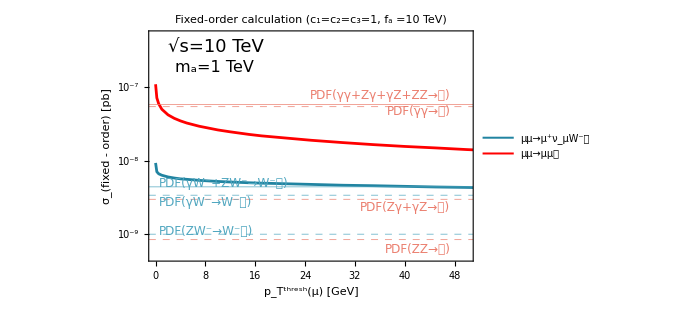

```mathematica
xsplot=ListLogPlot[{xs2to4data,xs2to3data,VBFdata,VBFgammagammadata,VBFzadata,VBFzzdata,VBSwadata,VBSwzdata,VBSdata},Joined->True,PlotRange->{{-0.1,50},{5*10^-10,5*10^-7}},PlotStyle->{{ColorData[24][6],Thickness[0.004]},{Red,Thickness[0.004]},{ColorData[24][1],Thickness[0.001]},{ColorData[24][1],Thickness[0.001],Dashed},{ColorData[24][1],Thickness[0.001],Dashed},{ColorData[24][1],Thickness[0.001],Dashed},{ColorData[24][5],Thickness[0.001],Dashed},{ColorData[24][5],Thickness[0.001],Dashed},{ColorData[24][5],Thickness[0.001]}},PlotLabel->Style["Fixed-order calculation (c_1=c_2=c_3=1, f_a =10 TeV)",Black,18,FontFamily->"Times"],Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style[Row[{Subsuperscript[p,"T",Style["thresh",Plain]],"(μ) [",Style["GeV",Plain],"]"}],Black,18,FontFamily->"Times"],Style["σ_(fixed - order) [pb]",Black,18,FontFamily->"Times"]},PlotLegends->{Placed[LineLegend[{Style[Row[{"μμ→μ^+ν_μ",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎"}],Black,15,FontFamily->"Times"],Style["μμ→μμ𝑎",Black,15,FontFamily->"Times"]},LegendLayout->{"Row",2}],{{0.68,0.83},{0.0,0.3}}]},Epilog->{Text[Style["√s=10 TeV",Black,18,FontFamily->"Times"],Scaled[{0.06,0.93}],Left,{1,0}],Text[Style["m_a=1 TeV",Black,16,FontFamily->"Times"],Scaled[{0.08,0.84}],Left,{1,0}],Text[Style[Row[{"PDF(",Superscript["γW","-"],"+",Superscript["ZW","-"],"→",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎)"}],ColorData[24][5],12,FontFamily->"Times"],Scaled[{0.03,0.335}],Left,{1,0}],Text[Style[Row[{"PDF(",Superscript["γW","-"],"→",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎)"}],ColorData[24][5],12,FontFamily->"Times"],Scaled[{0.03,0.255}],Left,{1,0}],Text[Style[Row[{"PDF(",Superscript["ZW","-"],"→",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎)"}],ColorData[24][5],12,FontFamily->"Times"],Scaled[{0.03,0.13}],Left,{1,0}],Text[Style["PDF(γγ+Zγ+γZ+ZZ→𝑎)",ColorData[24][1],12,FontFamily->"Times"],Scaled[{0.93,0.72}],Right,{1,0}],Text[Style["PDF(γγ→𝑎)",ColorData[24][1],12,FontFamily->"Times"],Scaled[{0.93,0.65}],Right,{1,0}],Text[Style["PDF(Zγ+γZ→𝑎)",ColorData[24][1],12,FontFamily->"Times"],Scaled[{0.93,0.235}],Right,{1,0}],Text[Style["PDF(ZZ→𝑎)",ColorData[24][1],12,FontFamily->"Times"],Scaled[{0.93,0.05}],Right,{1,0}]},ImageSize->500]
```

```mathematica
Row[{"μμ→μ^+ν_μ",Superscript[Style["W",FontSlant->"Plain"],"-"],"a)"}]
```

μμ→μ^+ν_μW^-a)

## No photon-photon fusion: c1=-c2

```mathematica
pt2to3={0,0.2,0.5,1,2,3,4,5,7,10,12,15,17,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,200,300,400,500,600,700,800,900,1000};
pt2to4={0,0.2,0.5,1,2,3,4,5,7,10,12,15,17,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,200,300,400,500,600,700,800,900,1000};
xs2to3={2.35,1.94,1.766,1.63,1.49,1.42,1.36,1.32,1.25,1.18,1.144,1.104,1.08,1.05,0.999,0.966,0.93,0.902,0.876,0.85,0.828,0.806,0.787,0.767,0.746,0.729,0.711,0.695,0.68,0.664(*100GeV*),0.429,0.296,0.216,0.161,0.122,0.094,0.0734,0.0576,0.0454}*10^-6/100(*rescale fa from 1TeV to 10TeV*);
xs2to4={9.36,7.12,6.68,6.37,6.05,5.87,5.71,5.59,5.41,5.26(*10*),5.15,5.05,4.99,4.9,4.77,4.67,4.59,4.51,4.42,4.35(*50*),4.28,4.22,4.16,4.10,4.05,4.01,3.94,3.89,3.84,3.80(*100*),3.08(*200GeV*),2.6,2.24,1.96,1.73,1.53,1.37,1.23,1.1}*10^-7/100(*rescale fa from 1TeV to 10TeV*);
```

```mathematica
xs2to4data=Table[{pt2to4[[i]],xs2to4[[i]]},{i,1,Length[pt2to4]}];
xs2to3data=Table[{pt2to3[[i]],xs2to3[[i]]},{i,1,Length[pt2to3]}];
VBSdata={{-10,3.65*10^-7/100+1.28*10^-7/100},{10000,3.65*10^-7/100+1.28*10^-7/100}};
VBSwadata={{-10,3.65*10^-7/100},{10000,3.65*10^-7/100}};
VBSwzdata={{-10,1.28*10^-7/100},{10000,1.28*10^-7/100}};

VBFdata={{-10,2*5.3*10^-7/100+5.9*10^-8/100},{10000,2*5.3*10^-7/100+5.9*10^-8/100}};
(*VBFgammagammadata={{-10,5.39*10^-6/100},{10000,5.39*10^-6/100}};*)
VBFzadata={{-10,2*5.3*10^-7/100},{10000,2*5.3*10^-7/100}};
VBFzzdata={{-10,5.9*10^-8/100},{10000,5.9*10^-8/100}};
```

#### plot

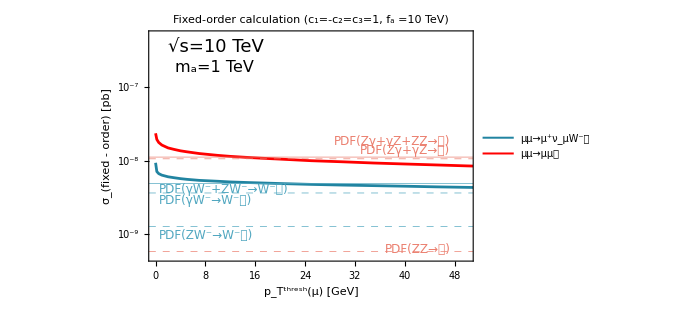

```mathematica
xsplot=ListLogPlot[{xs2to4data,xs2to3data,VBFdata(*,VBFgammagammadata*),VBFzadata,VBFzzdata,VBSwadata,VBSwzdata,VBSdata},Joined->True,PlotRange->{{-0.1,50},{5*10^-10,5*10^-7}},PlotStyle->{{ColorData[24][6],Thickness[0.004]},{Red,Thickness[0.004]},{ColorData[24][1],Thickness[0.001]},(*{Gray,Thickness[0.001],Dashed},*){ColorData[24][1],Thickness[0.001],Dashed},{ColorData[24][1],Thickness[0.001],Dashed},{ColorData[24][5],Thickness[0.001],Dashed},{ColorData[24][5],Thickness[0.001],Dashed},{ColorData[24][5],Thickness[0.001]}},PlotLabel->Style["Fixed-order calculation (c_1=-c_2=c_3=1, f_a =10 TeV)",Black,18,FontFamily->"Times"],Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style[Row[{Subsuperscript[p,"T",Style["thresh",Plain]],"(μ) [",Style["GeV",Plain],"]"}],Black,18,FontFamily->"Times"],Style["σ_(fixed - order) [pb]",Black,18,FontFamily->"Times"]},PlotLegends->{Placed[LineLegend[{Style[Row[{"μμ→μ^+ν_μ",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎"}],Black,15,FontFamily->"Times"],Style["μμ→μμ𝑎",Black,15,FontFamily->"Times"]},LegendLayout->{"Row",2}],{{0.68,0.83},{0.0,0.3}}]},Epilog->{Text[Style["√s=10 TeV",Black,18,FontFamily->"Times"],Scaled[{0.06,0.93}],Left,{1,0}],Text[Style["m_a=1 TeV",Black,16,FontFamily->"Times"],Scaled[{0.08,0.84}],Left,{1,0}],Text[Style[Row[{"PDF(",Superscript["γW","-"],"+",Superscript["ZW","-"],"→",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎)"}],ColorData[24][5],12,FontFamily->"Times"],Scaled[{0.03,0.31}],Left,{1,0}],Text[Style[Row[{"PDF(",Superscript["γW","-"],"→",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎)"}],ColorData[24][5],12,FontFamily->"Times"],Scaled[{0.03,0.265}],Left,{1,0}],Text[Style[Row[{"PDF(",Superscript["ZW","-"],"→",Superscript[Style["W",FontSlant->"Plain"],"-"],"𝑎)"}],ColorData[24][5],12,FontFamily->"Times"],Scaled[{0.03,0.112}],Left,{1,0}],Text[Style["PDF(Zγ+γZ+ZZ→𝑎)",ColorData[24][1],12,FontFamily->"Times"],Scaled[{0.93,0.52}],Right,{1,0}],(*Text[Style["PDF(γγ→𝑎)",Gray,12,FontFamily->"Times"],Scaled[{0.93,0.27}],Right,{1,0}],*)Text[Style["PDF(Zγ+γZ→𝑎)",ColorData[24][1],12,FontFamily->"Times"],Scaled[{0.93,0.48}],Right,{1,0}],Text[Style["PDF(ZZ→𝑎)",ColorData[24][1],12,FontFamily->"Times"],Scaled[{0.93,0.05}],Right,{1,0}]},ImageSize->500]
```